# The distribution of amino acid changes in different species

Analysis and comparison of A=to-I RNA editing in cephalopod species (squids and octopuses) and humans.

Zhamilya Bilyalova, Jun. 24,  2018

## Introduction: What is RNA editing?

RNA editing is a process that changes a RNA transcript such that it would no longer correspond to a sequence of DNA in a genome. There are many types of changes. A-to-I RNA editing is widespread in animals and results in the modification of a adenosine to inosine which will be read as a guanine. Nucleotides are being changed by enzymes that catalyze the editing.

Nucleobases that participate in A-to-I editing in mRNA:

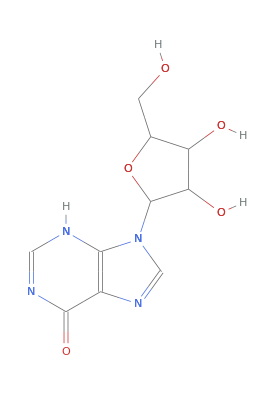
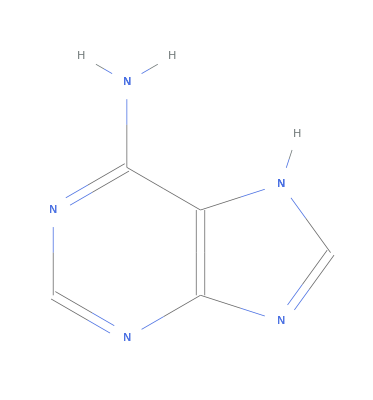
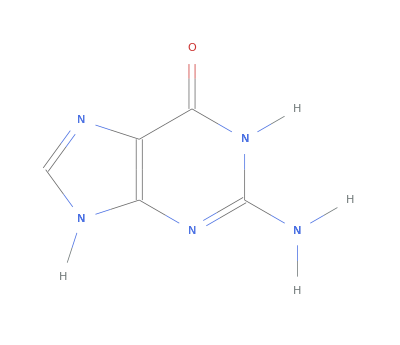
-Graphics-Inosine | -Graphics-Adenine | -Graphics-Guanine

```mathematica
Grid[{Map[Labeled[ChemicalData[#],#,Left]&,{"Inosine","Adenine","Guanine"}]},Spacings->2]
```

A-to-I editing in messenger RNA (mRNA) can cause changes in the amino acid sequence of a protein (amino acid recoding). Codons, 64 combinations in total, are codes for specific amino acids (one amino acid can relate to more than one codon).

To find what codons correspond to a specific amino acid, we can implement this code: An example is given for amino acid glycine:

```mathematica
Entity["Chemical","Glycine"][EntityProperty["Chemical","Codons"]]
```

{GGU,GGC,GGA,GGG}

Properties of a specific amino acid:

```mathematica
Entity["Chemical","Glycine"]["Properties"];
```

And this is a table of amino acids and their corresponding codons: header

```mathematica
Grid[Map[{#,#[EntityProperty["Chemical","Codons"]]}&,
Interpreter["Chemical"][{"Ser","Gly","Cys","Phe",
"Leu","Tyr","tryptophan","Arg","histidine","Gln","Pro",
"Ile","Met","Val","Ala","Asn","Lys","Asp","Glu"}]],
Frame->All]
```

L-serine | {UCU,UCC,UCA,UCG,AGU,AGC}
glycine | {GGU,GGC,GGA,GGG}
L-cysteine | {UGU,UGC}
L-phenylalanine | {UUU,UUC}
L-leucine | {UUA,UUG,CUU,CUC,CUA,CUG}
L-tyrosine | {UAU,UAC}
L-tryptophan | {UGG}
L-arginine | {CGU,CGC,CGA,CGG,AGA,AGG}
L-histidine | {CAU,CAC}
L-glutamine | {CAA,CAG}
L-proline | {CCU,CCC,CCA,CCG}
L-isoleucine | {AUU,AUC,AUA}
L-methionine | {AUG}
L-valine | {GUU,GUC,GUA,GUG}
L-alanine | {GCU,GCC,GCA,GCG}
L-asparagine | {AAU,AAC}
L-lysine | {AAA,AAG}
L-aspartic acid | {GAU,GAC}
L-glutamic acid | {GAA,GAG}

## Goal of this essay and description of the data

It was recently discovered that RNA editing and amino acid changes are widespread in cephalopods. In this essay, I attempt to analyse and compare the distribution of amino acid changes in cephalopod species (Squid, Sepia, Octopus vulgaris, Octopus bimaculoides) and human.

The data set consists of calculated expected distribution ("Expected amount", "Expected frequency") and observed distribution ("Edits", "Frequency") of amino acid changes in humans, four cephalopod species, and conserved edits from those species. KR  represents a change from amino acid K to amino acid R. "syn" means synonymous, does not make any changes to amino acid and is likely to not have an effect. "stop_W" means stop to w and causes a significant change in a protein sequence.

### Data

```mathematica
data=SemanticImport@URLDownload["https://github.com/ZhamilyaB/Summer2018Starter/raw/master/editingcodonsimplifieddata.csv"]
```

Dataset[<>]

```mathematica
datagrouped=data[GroupBy["Species"]]
```

Dataset[<>]

All types of amino acids changes are categorized as either radical or conserved. Radical changes are those that change the physicochemical property of the amino acid while conservative changes do not. The ratio of radical to conservative changes indicates how many changes are likely to have a negative effect.

```mathematica
radcon=Dataset[{
<|"Change"->"YC","A"->"R","B"->"R","C"-> "R"|>,<|"Change"->"TA","A"->"C","B"->"C","C"-> "C"|>,
<|"Change"->"syn","A"->"","B"->"","C"-> ""|>,<|"Change"->"SG","A"->"C","B"->"C","C"-> "C"|>,
<|"Change"->"RG","A"->"R","B"->"R","C"-> "R"|>,<|"Change"->"QR","A"->"C","B"->"R","C"-> "R"|>,
<|"Change"->"pW","A"->"","B"->"","C"-> ""|>,<|"Change"->"NS","A"->"C","B"->"R","C"-> "C"|>,
<|"Change"->"ND","A"->"R","B"->"C","C"-> "R"|>,<|"Change"->"MV","A"->"C","B"->"C","C"-> "C"|>,
<|"Change"->"KR","A"->"C","B"->"C","C"-> "C"|>,<|"Change"->"KE","A"->"R","B"->"R","C"-> "R"|>,
<|"Change"->"IV","A"->"C","B"->"C","C"-> "C"|>,<|"Change"->"IM","A"->"C","B"->"C","C"-> "C"|>,
<|"Change"->"HR","A"->"C","B"->"C","C"-> "C"|>,<|"Change"->"EG","A"->"R","B"->"R","C"-> "R"|>,
<|"Change"->"DG","A"->"R","B"->"R","C"-> "R"|>}]
```

Dataset[<>]

### Assumptions

Amino acid changes also can be random or non-random:  Random edits are likely to be slightly bad and don’t make an animal better, Non-random edits are likely to be good, be actively preserved in the population and seen more in conserved. In humans most changes are random, therefore, they are most likely to have a negative effect. In Individual cephalopod species, amino acid changes are a lot less random and they are less likely to have a negative effect. In conserved, changes are least random  and most likely to have a positive effect.

## Visualisation and Exploration

#### Expected frequency vs. actual frequency

```mathematica
MapThread[{image, {-Graphics-,-Graphics-,"Conserved cephalopods",-Graphics-,-Graphics-,-Graphics-}}]
```

```mathematica
coloredAmino=<|"KR"->RGBColor[0.010563313554859288, 0.842598209242611, 0.28387676305890275],"SG"->RGBColor[0.27953532144977733, 0.4836435395506147, 0.42893085600422864],"IM"->RGBColor[0.550447550119203, 0.1376882171135425, 0.10417086466364123],"TA"->RGBColor[0.5007397164248966, 0.7840482366236328, 0.7045968561167071],"IV"->RGBColor[0.2073047547900564, 0.09766618304217212, 0.7900750170440545],"syn"-> Black,"MV"->RGBColor[0.7368627516800415, 0.9854810528894713, 0.16876607015856604],"HR"->RGBColor[0.6257486253643563, 0.18583347602533107, 0.08319093382232734],"NS"->RGBColor[0.9619547743747547, 0.5741162790544341, 0.1898822938015785],"ND"->RGBColor[0.2786813860224029, 0.8446411358513435, 0.5682812147647314],
"QR"->RGBColor[0.7161778051845769, 0.7079120059790731, 0.8547544010382961],"KE"->RGBColor[0.9204697991268052, 0.01247026853391442, 0.588547608246031],"EG"->RGBColor[0.5494103924690645, 0.28378601201396725, 0.9354421828064061],"RG"->RGBColor[0.7039543181525214, 0.4665112553665334, 0.9831352427359885],"YC"->RGBColor[0.5185946438295199, 0.3923872911409534, 0.20838843032037646],"DG"->RGBColor[0.965242919857114, 0.6592751425902181, 0.052085256107477385],"stop-W"->RGBColor[0.5034569251580197, 0.09809664422436004, 0.7443255369657586]|>;
```

```mathematica
legend=SwatchLegend[Values@coloredAmino,Keys@coloredAmino,LegendLabel->"Aminoacids changes",
LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5];
```

```mathematica
TabView[
Flatten@Table[species-> 
Labeled[
ListPlot[
MapThread[Style[#1,Values[#2]]&,{Values@Normal[datagrouped[[species,All,{"Expected_frequency","Frequency"}]]],
Normal@coloredAmino}],
PlotLegends->legend,
PlotStyle->PointSize[0.02],
ImageSize->Large],
{Style["Frequency",Bold],Style["Expected Frequency",Bold]},{Left, Bottom}, RotateLabel->True]
,{species,{"human","specific_sepia","conserved_cephalopods","specific_oct_bim","specific_squid","specific_oct_vul"}}]]
```

123456

For importing images I was using  Wolfram|Alpha Query, which is a very helpful tool to find correct images and more information on a subject right inside Mathematica.

Squid image

WolframAlphaQueryResults

```mathematica
Entity["Species","Order:Teuthida"][EntityProperty["Species","Image"]]
```

-Graphics-

#### The comparison of frequencies of changes in all species

With this plot we are trying to explore the amino acid changes that are

1) the most different and the most similar  in all of the species.

2) how and why are they different or similar?

3) and what is the general pattern?

```mathematica
rulesTicks=MapIndexed[#1->First[#2]&,{"KR","SG","IM","TA","IV","MV","HR","NS","ND","QR","KE","EG","RG","YC",
"DG","stop-W","syn"}]
```

{KR→1,SG→2,IM→3,TA→4,IV→5,MV→6,HR→7,NS→8,ND→9,QR→10,KE→11,EG→12,RG→13,YC→14,DG→15,stop-W→16,syn→17}

```mathematica
rulesColors={"KR"->Blue}
```

{KR→RGBColor[0, 0, 1]}

```mathematica
rules=Join[rulesTicks,rulesColors]
```

{KR→1,SG→2,IM→3,TA→4,IV→5,MV→6,HR→7,NS→8,ND→9,QR→10,KE→11,EG→12,RG→13,YC→14,DG→15,stop-W→16,syn→17,KR→RGBColor[0, 0, 1]}

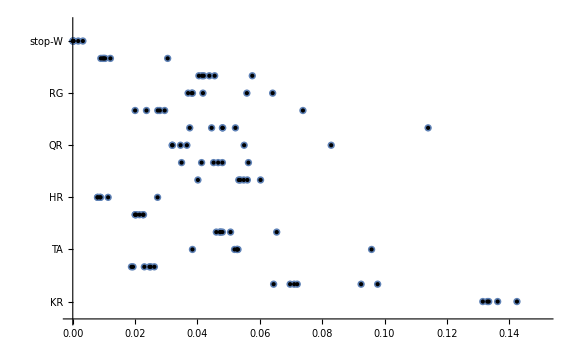
-Graphics-ChangesFrequency

```mathematica
Labeled[ListPlot[
MapThread[Style[{#2,#1},#3]&,Transpose@Values[Normal[data[All,{"Change","Frequency","Species"}]]]/.rules],
Ticks->{Automatic,Transpose@{Values[rulesTicks],Keys[rulesTicks]}},
ImageSize->Large],{Style["Changes",Bold],Style["Frequency",Bold]},{Left, Bottom}, RotateLabel->True]
```

First observation:
Humans have a different pattern from each one of cephalopod species, but cephalopod species together have a similar pattern which means that this amino acid preference is connected to cephalopod species being special.

```mathematica
rulesTicks=MapIndexed[#1->First[#2]&,{"KR","SG","IM","TA","IV","MV","HR","NS","ND","QR","KE","EG","RG","YC",
"DG","stop-W","syn"}]
```

{KR→1,SG→2,IM→3,TA→4,IV→5,MV→6,HR→7,NS→8,ND→9,QR→10,KE→11,EG→12,RG→13,YC→14,DG→15,stop-W→16,syn→17}

```mathematica
rulesColors={"KR"->Blue}
```

{KR→RGBColor[0, 0, 1]}

```mathematica
rules=Join[rulesTicks,rulesColors]
```

{KR→1,SG→2,IM→3,TA→4,IV→5,MV→6,HR→7,NS→8,ND→9,QR→10,KE→11,EG→12,RG→13,YC→14,DG→15,stop-W→16,syn→17,KR→RGBColor[0, 0, 1]}

```mathematica
Labeled[ListPlot[
MapThread[Style[{#2,#1},#3]&,Transpose@Values[Normal[data[All,{"Change","Frequency","Species"}]]]/.rules],
Ticks->{Automatic,Transpose@{Values[rulesTicks],Keys[rulesTicks]}},
ImageSize->Large],{Style["Changes",Bold],Style["Frequency",Bold]},{Left, Bottom}, RotateLabel->True]
```

-Graphics-ChangesFrequency

Second observation:
EG, TA, KE changes in human are most different and therefore are more likely to have a negative effect. As well contributed to cephalopod species being special.
If we check these three changes, it turns out: EG, KE are radical changes and TA is conserved.

#### The comparison of amount of changes in cephalopod species

```mathematica
rulesTicks=MapIndexed[#1->First[#2]&,{"KR","SG","IM","TA","IV","MV","HR","NS","ND","QR","KE","EG","RG","YC",
"DG","stop-W","syn"}]
```

{KR→1,SG→2,IM→3,TA→4,IV→5,MV→6,HR→7,NS→8,ND→9,QR→10,KE→11,EG→12,RG→13,YC→14,DG→15,stop-W→16,syn→17}

```mathematica
rulesColors={"KR"->Blue}
```

{KR→RGBColor[0, 0, 1]}

```mathematica
rules=Join[rulesTicks,rulesColors]
```

{KR→1,SG→2,IM→3,TA→4,IV→5,MV→6,HR→7,NS→8,ND→9,QR→10,KE→11,EG→12,RG→13,YC→14,DG→15,stop-W→16,syn→17,KR→RGBColor[0, 0, 1]}

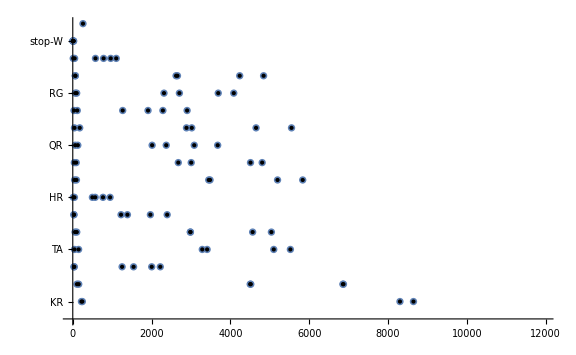
-Graphics-ChangesEdits

```mathematica
Labeled[ListPlot[
MapThread[Style[{#2,#1},#3]&,Transpose@Values[Normal[data[All,{"Change","Edits","Species"}]]]/.rules],
Ticks->{Automatic,Transpose@{Values[rulesTicks],Keys[rulesTicks]}},
ImageSize->Large],{Style["Changes",Bold],Style["Edits",Bold]},{Left, Bottom}, RotateLabel->True]
```

Observation:
Squid and sepia have more similar number of edits compared to oct_bim and oct_vul because they are just different kinds of octopus.

Function::slotn: Slot number 3 in Style[{#2,#1},#3]& cannot be filled from (Style[{#2,#1},#3]&)[1,220].

Function::slotn: Slot number 3 in Style[{#2,#1},#3]& cannot be filled from (Style[{#2,#1},#3]&)[2,151].

Function::slotn: Slot number 3 in Style[{#2,#1},#3]& cannot be filled from (Style[{#2,#1},#3]&)[3,38].

General::stop: Further output of Function::slotn will be suppressed during this calculation.

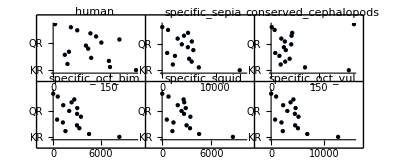
-Graphics-ChangesEdits

```mathematica
Labeled[GraphicsGrid[Partition[Flatten@Table[ListPlot[
MapThread[Style[{#2,#1},#3]&,Transpose@Values[Normal[datagrouped[species,All,{"Change","Edits"}]]]/.rules],
DataRange->{0,15000},
PlotLabel->StringForm[species],
Ticks->{Automatic,Transpose@{Values[rulesTicks],Keys[rulesTicks]}},
ImageSize->Large,PlotStyle->PointSize[Medium]],
{species,{"human","specific_sepia","conserved_cephalopods","specific_oct_bim","specific_squid","specific_oct_vul"}}],
3],Frame-> All, ImageSize->Full], {Style["Changes",Bold],Style["Edits",Bold]},{Left, Bottom}, RotateLabel->True]
```

#### Frequencies in different species

How are the distribution different/similar between different species?

```mathematica
rulesTicksspecies=MapIndexed[#1->First[#2]&,{"human","specific_sepia","conserved_cephalopods",
"specific_oct_bim","specific_squid","specific_oct_vul"}]
```

{human→1,specific_sepia→2,conserved_cephalopods→3,specific_oct_bim→4,specific_squid→5,specific_oct_vul→6}

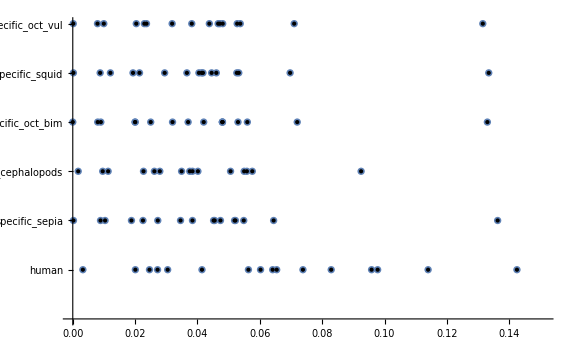
-Graphics-SpeciesFrequency

```mathematica
Labeled[ListPlot[
MapThread[Style[{#2,#1},#3]&,Transpose@Values[Normal[data[All,{"Species","Frequency","Change"}]]]/.rulesTicksspecies],
Ticks->{Automatic,Transpose@{Values[rulesTicksspecies],Keys[rulesTicksspecies]}}, ImageSize->Large],
{Style["Species",Bold],Style["Frequency",Bold]},{Left, Bottom}, RotateLabel->True]
```

First, we notice that KR and synonymous are conserved. We can observe that they have higher frequency in cephalopod species which means that the ratio of radical to conserved in cephalopod species is less than this ratio in humans and conserved_cephalopods.
Which is exactly the difference in ratios of radical to conserved in all the species from the research:

Ratio of radical to conserved:     -Graphics-

## Further explorations

Trade-off between Transcriptome Plasticity and Genome Evolution in Cephalopods, Cell 169, 191–202 (2017).

## Author contact information

zhamilya.bilyalova@prismsus.org